```mathematica
Статистика аэродромов(ВПП)
```

```mathematica
Грунтовые ВПП
Европа
```

{{Albania,1},{Luxembourg,1},{Cyprus,2},{Montenegro,2},«32»,{France,178},{United Kingdom,199},{Germany,220},{Ukraine,236}}

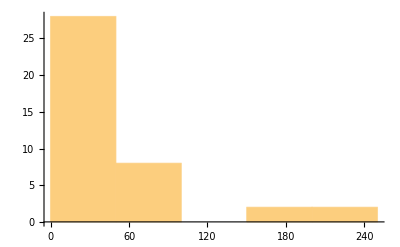

```mathematica
airportData = DeleteCases[Table[{country,CountryData[country,"UnpavedAirports"]},{country,CountryData["Europe"]}], {_, _Missing}];
Short[SortBy[airportData, Last]]
Histogram[airportData[[All,2]]]
```

```mathematica
Наибольшие значения:
```

```mathematica
TakeLargest[airportData [[All,2]],10]
```

{621,519,183,169,137,118,99,80,75,57}

```mathematica
Азия
```

{{Afghanistan,35},{Armenia,1},{Azerbaijan,7},{Bangladesh,2},{Bhutan,1},{Brunei,0},{Cambodia,14},{China,57},{East Timor,4},{Egypt,13},{Gaza Strip,0},{Georgia,4},«24»,{South Korea,44},{Sri Lanka,2},{Syria,75},{Taiwan,4},{Tajikistan,8},{Thailand,41},{Turkey,12},{Turkmenistan,7},{United Arab Emirates,14},{Uzbekistan,27},{Vietnam,6},{Yemen,37}}

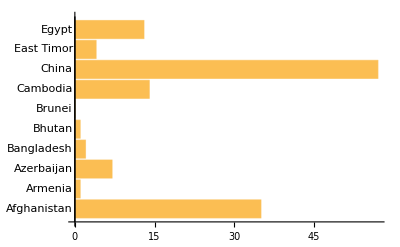

```mathematica
asianAirports = DeleteCases[Table[{country,CountryData[country,"UnpavedAirports"]},{country,CountryData["Asia"]}], {_, _Missing}];
Short[SortBy[asianAirports, Greater]]
topTenAirports = Take[SortBy[africanAirports, Greater], 10];
BarChart[topTenAirports[[All,2]], ChartLabels->topTenAirports[[All,1]], BarOrigin-> Left]
```

```mathematica
Наибольшие значения:
```

```mathematica
TakeLargest[africanAirports [[All,2]],10]
```

{621,519,183,169,137,118,99,80,75,57}

```mathematica
Получим общее количество аэропортов и среднее значение:
```

```mathematica
asianAirports = DeleteCases[Table[{country,CountryData[country,"UnpavedAirports"]},{country,CountryData["Asia"]}], {_, _Missing}];
asianAirportAmounts = asianAirports[[All,2]];
Total[asianAirportAmounts]
Mean[asianAirportAmounts]
```

2702

1351/24

```mathematica
Сравним количество аэропортов
```

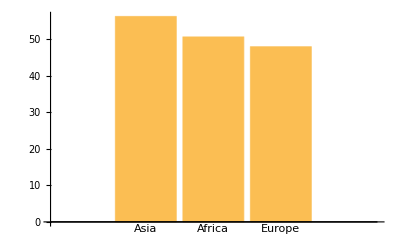

```mathematica
asianAirports = DeleteCases[Table[{country,CountryData[country,"UnpavedAirports"]},{country,CountryData["Asia"]}], {_, _Missing}];
africanAirports = DeleteCases[Table[{country,CountryData[country,"UnpavedAirports"]},{country,CountryData["Africa"]}], {_, _Missing}];
europeanAirports = DeleteCases[Table[{country,CountryData[country,"UnpavedAirports"]},{country,CountryData["Europe"]}], {_, _Missing}];

BarChart[{Mean[asianAirports[[All,2]]], Mean[africanAirports[[All,2]]], Mean[europeanAirports[[All,2]]]}, ChartLabels -> {"Asia", "Africa", "Europe"}]
```

```mathematica
Узнаем зависимость количества аэродромов от ВВП
```

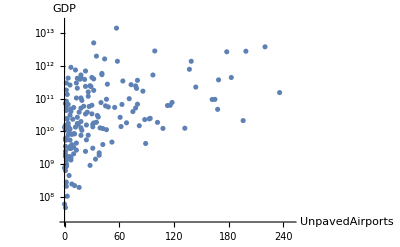

```mathematica
data = Table[Tooltip[{CountryData[i, "UnpavedAirports"], CountryData[i, "GDP"]}, CountryData[i, "Name"]], {i, CountryData[]}];
ListLogPlot[data, AxesLabel-> {"UnpavedAirports", "GDP"}]
```

```mathematica
Зависимость количества грунтовый аэропортов от аэропотов в целом.
```

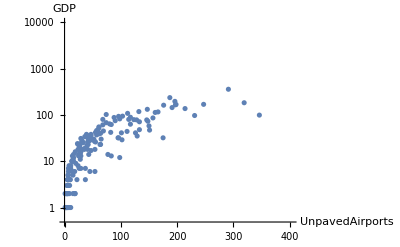

```mathematica
data = Table[Tooltip[{CountryData[i, "Airports"], CountryData[i, "UnpavedAirports"]}, CountryData[i, "Name"]], {i, CountryData[]}];
ListLogPlot[data, AxesLabel-> {"UnpavedAirports", "GDP"}]
```

```mathematica
Manipulate[plotFn[Table[Tooltip[{CountryData[i, "Airports"], CountryData[i, property]}, CountryData[i,"Name"]], {i, CountryData[All]}], AxesLabel -> {"GDP", property}],
{property, {"UnpavedAirports", "GDP", "LiteracyFraction"}},
{{plotFn, ListLogLogPlot}, {ListPlot, ListLogPlot, ListLogLogPlot}}, SaveDefinitions-> True]
```